```mathematica
SetDirectory[NotebookDirectory[]];
```

## Bar

```mathematica
xMin=0.5;
xMax=4.2;
yMin=0;
yMax=0.2;
xMax2=xMax-xMin;
dx=0.1;
dy=0.5;
dy2=0.15;
dy3=0.22;
cfCHI2=(Blend[{{0,Black},{100,White}},#]&);
barCHI2=Graphics[{
{Raster[{Range[0,100,1/1000]},{{xMin,yMin},{xMax,yMax}},ColorFunction->cfCHI2]},AbsoluteThickness[cm[0.02]],Line[{{xMin,yMin},{xMax,yMin},{xMax,yMax},{xMin,yMax},{xMin,yMin}}],
Line[{{xMin+0/4*xMax2,0},{xMin+0/4*xMax2,-dy2}}],
Line[{{xMin+1/4*xMax2,0},{xMin+1/4*xMax2,-dy2}}],
Line[{{xMin+2/4*xMax2,0},{xMin+2/4*xMax2,-dy2}}],
Line[{{xMin+3/4*xMax2,0},{xMin+3/4*xMax2,-dy2}}],
Line[{{xMin+1*xMax2,0},{xMin+1*xMax2,-dy2}}],
Inset[Style["0",FontFamily->"Helvetica",FontSize->7],{xMin+0/4*xMax2,-dy3},{Center,Top}],
Inset[Style["25",FontFamily->"Helvetica",FontSize->7],{xMin+1/4*xMax2,-dy3},{Center,Top}],
Inset[Style["50",FontFamily->"Helvetica",FontSize->7],{xMin+2/4*xMax2,-dy3},{Center,Top}],
Inset[Style["75",FontFamily->"Helvetica",FontSize->7],{xMin+3/4*xMax2,-dy3},{Center,Top}],
Inset[Style["100",FontFamily->"Helvetica",FontSize->7],{xMin+4/4*xMax2,-dy3},{Center,Top}]




},PlotRange->{{0,xMax+xMin},{yMin-2*dy,yMax+dy}},ImageSize->cm[xMax+xMin],ImagePadding->0]
```

-Graphics-

## Panels

```mathematica
BP[n_]:=Max[n]/Total[n]
gini[x_]:=N[Sum[Sum[Abs[x[[i]]-x[[j]]],{j,1,Length[x]}],{i,1,Length[x]}]/(2*Length[x]*Sum[x[[j]],{j,1,Length[x]}])]
shannon[n_]:=(
Sh=0;
NN=Total[n];
Do[Sh-=n[[i]]/NN*Log[n[[i]]/NN],{i,1,Length[n]}];
N[Sh]
)
JE[n_]:=shannon[n]/Log[Length[n]]
TT[n_]:=Log[Length[n]]-shannon[n]
Sr[n_]:=(NN=Total[n];∑_(i=1)^Length[n] (n[[i]]/NN)^2)
H[n_]:=(nM=Mean[n];1/2*(∑_(i=1)^Length[n] Abs[n[[i]]-nM])/(∑_(i=1)^Length[n] n[[i]]))
getTheoryData[pi_,pt_,pr_,pd_,n_]:=(
fileName="diversity_pi_"<>ToString[pi]<>"_pt_"<>ToString[pt]<>"_pr_"<>ToString[pr]<>"_pd_"<>ToString[pd]<>"_.dat";
a=Import["FFM//output//diversity//"<>fileName,"Table"];
out={};
Do[
nnn=a[[i]][[-1]];
If[nnn≥2,
AppendTo[out,{a[[i]][[1]],a[[i]][[2*n]],a[[i]][[2*n + 1]]*√(nnn/(nnn-1)),nnn}],
AppendTo[out,{a[[i]][[1]],a[[i]][[2*n]],-1,nnn}]

],{i,2,1001}];
out
)
chi2[pi_,pt_,pr_,pd_,n_,f_]:=(
theoryData=getTheoryData[pi,pt,pr,pd,n];
χ2=0.;
Do[
c=Import["chambers//c"<>ToString[j]<>".dat","List"];
cellNumber=Total[c];
If[cellNumber>61,
numTheory=theoryData[[cellNumber]][[-1]];
If[numTheory≥2,
meanTheory=theoryData[[cellNumber]][[2]];
stdTheory=theoryData[[cellNumber]][[3]];
meanExperiment=N[f[c]];
χ2+=(meanTheory-meanExperiment)^2/stdTheory^2,
χ2+=10000
];
]
,{j,1,21}];
χ2
)
chi2Mean[pi_,pt_,pr_,pd_]:=(
Mean[
{
chi2[pi,pt,pr,pd,8,BP],
chi2[pi,pt,pr,pd,1,gini],
chi2[pi,pt,pr,pd,2,shannon],
chi2[pi,pt,pr,pd,4,JE],
chi2[pi,pt,pr,pd,5,TT],
chi2[pi,pt,pr,pd,6,Sr],
chi2[pi,pt,pr,pd,9,H]
}])
```

```mathematica
fixNum[num_]:=(
If[StringCount[num,"e"]==1,ToExpression[StringTake[num,{1,-5}]]*10^-5.,ToExpression[num]]
)
plotChi[ptForPlot_]:=(
piList={
"1",
"0.1",
"0.01",
"0.001",
"0.0001",
"1e-05",

"0.562341",
"0.0562341",
"0.00562341",
"0.000562341",
"5.62341e-05",

"0.316228",
"0.0316228",
"0.00316228",
"0.000316228",
"3.16228e-05",

"0.177828",
"0.0177828",
"0.00177828",
"0.000177828",
"1.77828e-05"
};
prList={
"1",

"8.8914e-05",
"0.88914",
"0.088914",
"0.0088914",
"0.00088914",

"1.58114e-05",
"0.158114",
"0.0158114",
"0.00158114",
"0.000158114",

"2.81171e-05",
"0.281171",
"0.0281171",
"0.00281171",
"0.000281171",

"5e-05",
"0.5",
"0.05",
"0.005",
"0.0005"
};
chiOutList={};


size=3*6/5;

Do[
Print[j];
Do[
GG={
Log[fixNum[piList[[i]]]],
Log[fixNum[prList[[j]]]],chi2Mean[piList[[i]],ptForPlot,prList[[j]],0.026]
};
AppendTo[chiOutList,GG];
AppendTo[chiAllList,GG[[3]]];

,{i,1,Length[piList]}],{j,1,Length[prList]}];

b=ListDensityPlot[chiOutList,ColorFunction->cfCHI2,ColorFunctionScaling->False,InterpolationOrder->0,PlotRange->{{Log[10^-5],Log[1]},{Log[1.58114*10^-5],Log[1]},{0,100}}];


(*Lines around experimentally comparable values*)
fLegend=5;
FigA=plotBack[
{b},
xTicks->  {Log[0.000001],Log[0.0001],Log[0.01],Log[1]},
yTicks->{Log[0.000001],Log[0.0001],Log[0.01],Log[1]},
xReplace->{Row[{Superscript[Style["10"],Style["-6",FontSize->fLegend]]}],Row[{Superscript[Style["10"],Style["-4",FontSize->4]]}],Row[{Superscript[Style["10"],Style["-2",FontSize->4]]}],Row[{Superscript[Style["10"],Style["0",FontSize->4]]}]
},
yReplace->{Row[{Superscript[Style["10"],Style["-6",FontSize->fLegend]]}],Row[{Superscript[Style["10"],Style["-4",FontSize->4]]}],Row[{Superscript[Style["10"],Style["-2",FontSize->4]]}],Row[{Superscript[Style["10"],Style["0",FontSize->4]]}]
},
tickLength->0.12,
plotRange->{
{Log[10^-5],Log[1]},{Log[1.58114*10^-5],Log[1]}},
plotDimensions->{3*6/5,3*6/5},
plotMargins->{1.2,0.6,1.2,1.2},
plotLabels->{
Row[{
Style["Spontaneous division probability "],Subscript[Style["p",Italic],Style["i",FontSize->fLegend]]}],
Row[{Style["Refractory probability "],Subscript[Style["p",Italic],Style["r",FontSize->fLegend]]}]},
labelsDistance->{0.6,0.8},
plotTitle->True,
titleText->Row[{Subscript[Style["p",Italic],Style["t",FontSize->fLegend]],
Style[" = "],Style[ptForPlot]}],
titleDistance->0.25,
fontMain->7,
fontName->"Helvetica"
]
)
```

```mathematica
ptList={0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1};
panels={};
source={};
chiAllList={};
Do[AppendTo[panels,plotChi[ptList[[iT]]]];Print[ptList[[iT]]],{iT,1,Length[ptList]}]
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

0.2

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

0.3

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

0.4

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

0.5

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

0.6

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

0.7

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

0.8

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

0.9

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

1

## Output

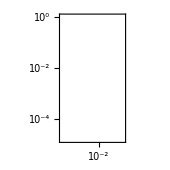
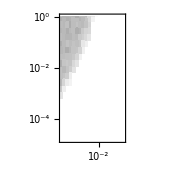
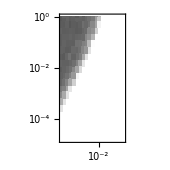
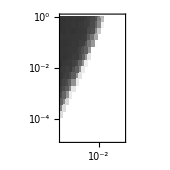
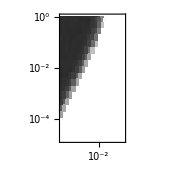
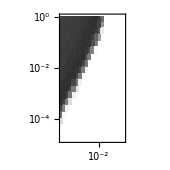
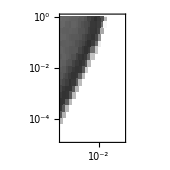
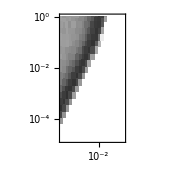
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
panels
```

## Figure

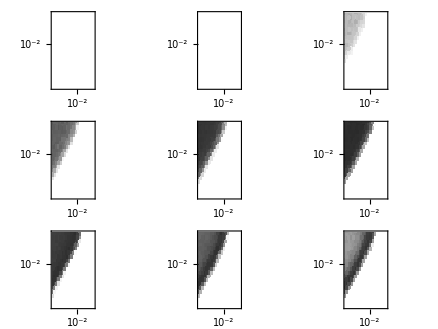

```mathematica
tCHI2=Row[{Style["⟨",FontFamily->"Helvetica",FontSize->7],Superscript[Style["χ",FontFamily->"Helvetica",FontSize->7],Style["2",FontFamily->"Helvetica",FontSize->5]],Style["⟩",FontFamily->"Helvetica",FontSize->7]}];
dX=5;
dY=-5;
dY2=-1.2;

FigED6=figure[15.5,16.8,
elements->Join[{tCHI2},{barCHI2},panels],
elementCoordinates->{
{1*dX+1.2+3*6/5/2,-0.6},
{1*dX+1.2+3*6/5/2,-1.3},

{0*dX,0*dY+dY2-0.5},
{1*dX,0*dY+dY2-0.5},
{2*dX,0*dY+dY2-0.5},
{0*dX,1*dY+dY2-0.5},
{1*dX,1*dY+dY2-0.5},
{2*dX,1*dY+dY2-0.5},
{0*dX,2*dY+dY2-0.5},
{1*dX,2*dY+dY2-0.5},
{2*dX,2*dY+dY2-0.5}
},
centeredElements->{1,2}]
```

```mathematica
Export["figs//SYS_ED_Fig6.pdf",FigED6]
```

figs//SYS_ED_Fig6.pdf